# Problem 3

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Times New Roman"}];
SetOptions[ListPlot,BaseStyle->{FontFamily->"Times New Roman"}];
```

```mathematica
p = 10^-4;
NSolve[Log[n]/n == p,n]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{n→1.0001},{n→116671.}}

```mathematica
Ncr = 116671;
kcrmed = N[(Ncr-1)p]
```

11.667

```mathematica
dmed = Log[Ncr]/Log[kcrmed]
```

4.74898

```mathematica
pbinom[k_,p_,n_]:=Binomial[n,k] p^k(1-p)^(n-1-k);
ppoisson[k_,kmed_,n_]:=kmed/(k!)Exp[-kmed];
```

```mathematica
binomtable=Table[{k,pbinom[k,0.0001,6000]},{k,0,6}];
poissontable=Table[{k,ppoisson[k,0.5999,6000]},{k,0,6}];
LP = ListPlot[{binomtable,poissontable},PlotRange->{{-0.05,6},{0,0.6}},PlotStyle->{{Thick,Orange},{Thick,Purple},{Thick,Orange},{Thick,Purple}},Frame->True,FrameStyle->Directive[Thick,Black,15],ImageSize->500,AspectRatio->9/16,FrameLabel->{"k","p_k"},LabelStyle->Directive[Black],PlotLegends->Placed[{"Binomial","Poisson"},{0.85,0.8}]];
```

```mathematica
PP =Plot[{pbinom[k,0.0001,6000],ppoisson[k,0.5999,6000]},{k,0,16},PlotRange->{{-0.05,6},{0,0.6}},PlotStyle->{{Thick,Orange},{Thick,Purple},{Thick,Orange},{Thick,Purple}},Frame->True,FrameStyle->Directive[Thick,Black,15],ImageSize->500,AspectRatio->9/16,FrameLabel->{"k","p_k"},LabelStyle->Directive[Black]];
```

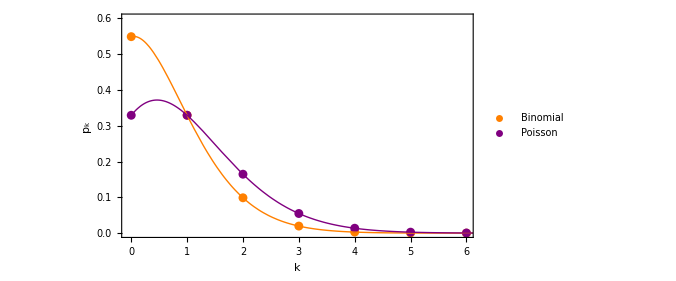

```mathematica
Show[LP,PP]
```

```mathematica
pbinom[4,0.0001,6000]
```

0.00296201

```mathematica
ppoisson[4,0.5999,6000]
```

0.0137194

```mathematica
ppoisson[4,0.5999,6000]/pbinom[4,0.0001,6000]
```

4.63178